```mathematica
SetDirectory["/home/dschiebe/Documents/lanayru/PhD_Files/HexaBox_102PureIntsDone"];
PureIntegralsOld=ReadList[FileNameJoin[{Directory[],"files/PureIntegralBasis1-138.txt"}]];
PureIntegralsNew=PureIntegralsOld;
Get[FileNameJoin[{Directory[],"HexaBoxModules.m"}]];
$P=2^31-1;
$P=2^31-1;
CayleyEntry[i_,j_]:=Module[{mat},
If[i==0 && j==0 ,
Return[0];
];
If[i==0 || j==0 ,
Return[1];
];

If[i==j,
mat=2msq[i]/.intMasses;
Return[mat];
];
If[i<j,
mat=((msq[i]/.intMasses)+(msq[j]/.intMasses)-Expand[(Sum[q[n],{n,i,j-1}])^2])/.mandelstamScalarProducts/.kinematics;
Return[mat];
];
If[i>j,
mat=CayleyEntry[j,i];
Return[mat];
];
]
cutCayley[mat_,l_]:=Module[{res},
res=mat;
res=Delete[res,l];
res=Transpose[Delete[Transpose[res],l]];
res
]
```

# Diagram 139/151 (Basis1 - 138)

hxb[-1,0,1,1,0,1,1,1,1,0,0,0,0]

hxb[0,0,1,1,0,1,1,1,1,0,0,0,0]

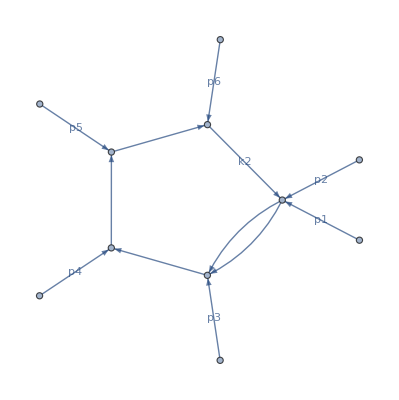

```mathematica
PureIntegralsOld[[139]]
PureIntegralsOld[[151]]
plotDiagram[PureIntegralsOld[[151]]]
```

```mathematica
q[1]=p[5]/.p4cons;
q[2]=p[4]/.p4cons;
q[3]=p[1]+p[2]+p[3]/.p4cons;
q[4]=-q[1]-q[2]-q[3];
intMasses={msq[1]->mt2,msq[2]->0,msq[3]->0,msq[4]->0};
modcayleyMat=Table[CayleyEntry[i,j],{i,1,4},{j,1,4}];
modcayleyMat//MatrixForm
kP=3+1;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]/.root[x_]:>root[Factor[x]]/.root[x_^2 y_^2]:>x y
 BasisChange[1]=ep^3/LS (1-2ep)
```

(2 mt2 | 0 | mt2-s45 | 0
0 | 0 | 0 | -s56
mt2-s45 | 0 | 0 | -s123
0 | -s56 | -s123 | 0)

1/(2 (mt2-s45) s56)

2 (1-2 ep) ep^3 (mt2-s45) s56

```mathematica
q[1]=p[5]/.p4cons;
q[2]=p[4];
q[3]=p[3];
q[4]=p[2]+p[1]/.p4cons;
q[5]=-q[1]-q[2]-q[3]-q[4];
intMasses={msq[1]->mt2,msq[2]->0,msq[3]->0,msq[4]->0,msq[5]->0};
modcayleyMat=Table[CayleyEntry[i,j],{i,0,5},{j,0,5}];
modcayleyMat//MatrixForm
kP=4;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]/.root[x_]:>root[-x]

vectors={q[1],q[2],q[3],q[4]};
Gram1=Det[Expand[Table[vectors[[i]]vectors[[j]],{i,1,4},{j,1,4}]]/.kinematics/.mandelstamScalarProducts];
vectors2={q[1],q[2],q[3],q[4],k[2]};
Baikov=Factor[Expand[Det[Expand[Table[vectors2[[i]]vectors2[[j]],{i,1,5},{j,1,5}]]/.loopMomentumScalarProducts/.kinematics/.mandelstamScalarProducts]]];

BasisChange[2]=ep^4/LS 1/PR[3]*(2*Baikov)/(Gram1*(d-4));
```

(0 | 1 | 1 | 1 | 1 | 1
1 | 2 mt2 | 0 | mt2-s45 | mt2-s345 | 0
1 | 0 | 0 | 0 | -s34 | -s56
1 | mt2-s45 | 0 | 0 | 0 | -s123
1 | mt2-s345 | -s34 | 0 | 0 | -s12
1 | 0 | -s56 | -s123 | -s12 | 0)

1/(2 root[mt2^2 s12^2-2 mt2^2 s12 s123+mt2^2 s123^2-2 mt2^2 s12 s34+2 mt2^2 s123 s34+2 mt2 s12 s123 s34-2 mt2 s123^2 s34+mt2^2 s34^2-2 mt2 s123 s34^2+s123^2 s34^2+2 mt2 s12 s123 s345-2 mt2 s123^2 s345-2 mt2 s123 s34 s345-2 s123^2 s34 s345+s123^2 s345^2-2 mt2 s12^2 s45+2 mt2 s12 s123 s45+4 mt2 s12 s34 s45-2 mt2 s123 s34 s45+2 s12 s123 s34 s45-2 mt2 s34^2 s45-2 s123 s34^2 s45-2 s12 s123 s345 s45+2 s123 s34 s345 s45+s12^2 s45^2-2 s12 s34 s45^2+s34^2 s45^2-2 mt2 s12 s345 s56+2 mt2 s123 s345 s56-2 mt2 s34 s345 s56+2 s123 s34 s345 s56-2 s123 s345^2 s56+2 mt2 s12 s45 s56-2 mt2 s123 s45 s56+2 mt2 s34 s45 s56-4 s12 s34 s45 s56+2 s123 s34 s45 s56+2 s12 s345 s45 s56+2 s123 s345 s45 s56+2 s34 s345 s45 s56-2 s12 s45^2 s56-2 s34 s45^2 s56+s345^2 s56^2-2 s345 s45 s56^2+s45^2 s56^2])

# Diagram 140/152 (Basis1 - 138)

hxb[-1,1,0,1,0,1,1,1,1,0,0,0,0]

hxb[0,1,0,1,0,1,1,1,1,0,0,0,0]

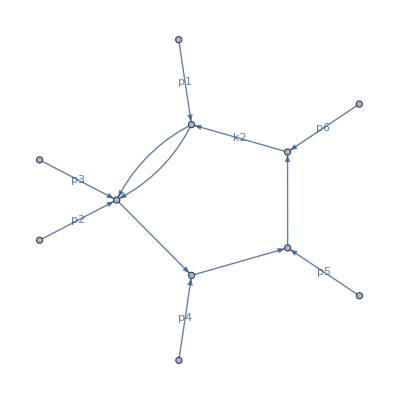

```mathematica
PureIntegralsOld[[140]]
PureIntegralsOld[[152]]
plotDiagram[PureIntegralsOld[[140]]]
```

```mathematica
q[1]=p[6]/.p4cons;
q[2]=p[1]+p[2]+p[3]/.p4cons;
q[3]=p[4]/.p4cons;
q[4]=-q[1]-q[2]-q[3];
intMasses={msq[1]->mt2,msq[2]->0,msq[3]->0,msq[4]->0};
modcayleyMat=Table[CayleyEntry[i,j],{i,1,4},{j,1,4}];
modcayleyMat//MatrixForm
kP=3+1;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]/.root[x_]:>root[Factor[x]]/.root[x_^2 y_^2]:>x y
 BasisChange[3]=ep^3/LS (1-2ep)
```

(2 mt2 | 0 | mt2-s45 | 0
0 | 0 | -s123 | -s56
mt2-s45 | -s123 | 0 | 0
0 | -s56 | 0 | 0)

1/(2 (mt2-s45) s56)

2 (1-2 ep) ep^3 (mt2-s45) s56

```mathematica
q[1]=p[5]/.p4cons;
q[2]=p[4];
q[3]=p[2]+p[3];
q[4]=p[1]/.p4cons;
q[5]=-q[1]-q[2]-q[3]-q[4];
intMasses={msq[1]->mt2,msq[2]->0,msq[3]->0,msq[4]->0,msq[5]->0};
modcayleyMat=Table[CayleyEntry[i,j],{i,0,5},{j,0,5}];
modcayleyMat//MatrixForm
kP=4;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]/.root[x_]:>root[-x]

vectors={q[1],q[2],q[3],q[4]};
Gram1=Det[Expand[Table[vectors[[i]]vectors[[j]],{i,1,4},{j,1,4}]]/.kinematics/.mandelstamScalarProducts];
vectors2={q[1],q[2],q[3],q[4],k[2]};
Baikov=Factor[Expand[Det[Expand[Table[vectors2[[i]]vectors2[[j]],{i,1,5},{j,1,5}]]/.loopMomentumScalarProducts/.kinematics/.mandelstamScalarProducts]]];

BasisChange[4]=ep^4/LS 1/PR[2]*(2*Baikov)/(Gram1*(d-4));
```

(0 | 1 | 1 | 1 | 1 | 1
1 | 2 mt2 | 0 | mt2-s45 | mt2-s16 | 0
1 | 0 | 0 | 0 | -s234 | -s56
1 | mt2-s45 | 0 | 0 | -s23 | -s123
1 | mt2-s16 | -s234 | -s23 | 0 | 0
1 | 0 | -s56 | -s123 | 0 | 0)

1/(2 root[mt2^2 s123^2-2 mt2 s123^2 s16+s123^2 s16^2+2 mt2^2 s123 s234-2 mt2 s123^2 s234-2 mt2 s123 s16 s234-2 s123^2 s16 s234+4 mt2 s123 s23 s234+mt2^2 s234^2-2 mt2 s123 s234^2+s123^2 s234^2-2 mt2 s123 s234 s45+2 s123 s16 s234 s45-2 mt2 s234^2 s45-2 s123 s234^2 s45+s234^2 s45^2+2 mt2 s123 s16 s56-2 s123 s16^2 s56-4 mt2^2 s23 s56+2 mt2 s123 s23 s56+4 mt2 s16 s23 s56+2 s123 s16 s23 s56-4 mt2 s23^2 s56-2 mt2 s16 s234 s56+2 s123 s16 s234 s56+2 mt2 s23 s234 s56-2 s123 s23 s234 s56-2 mt2 s123 s45 s56+2 s123 s16 s45 s56+4 mt2 s23 s45 s56-4 s16 s23 s45 s56+2 mt2 s234 s45 s56+2 s123 s234 s45 s56+2 s16 s234 s45 s56+2 s23 s234 s45 s56-2 s234 s45^2 s56+s16^2 s56^2-2 s16 s23 s56^2+s23^2 s56^2-2 s16 s45 s56^2-2 s23 s45 s56^2+s45^2 s56^2])

# Diagram 141/153 (Basis1 - 138)

hxb[-1,1,0,1,1,0,1,1,1,0,0,0,0]

hxb[0,1,0,1,1,0,1,1,1,0,0,0,0]

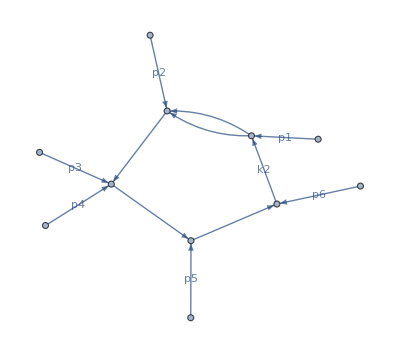

```mathematica
PureIntegralsOld[[141]]
PureIntegralsOld[[153]]
plotDiagram[PureIntegralsOld[[141]]]
```

```mathematica
q[1]=p[1]+p[2]/.p4cons;
q[2]=p[3]+p[4]/.p4cons;
q[3]=p[5]/.p4cons;
q[4]=-q[1]-q[2]-q[3];
intMasses={msq[1]->0,msq[2]->0,msq[3]->0,msq[4]->mt2};
modcayleyMat=Table[CayleyEntry[i,j],{i,1,4},{j,1,4}];
modcayleyMat//MatrixForm
kP=3+1;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]/.root[x_]:>root[Factor[x]]/.root[x_^2 y_^2]:>x y
BasisChange[5]=ep^3/LS (1-2ep)

q[1]=p[1]/.p4cons;
q[2]=p[2];
q[3]=p[3]+p[4];
q[4]=p[5]/.p4cons;
q[5]=-q[1]-q[2]-q[3]-q[4];
intMasses={msq[1]->0,msq[2]->0,msq[3]->0,msq[4]->0,msq[5]->mt2};
modcayleyMat=Table[CayleyEntry[i,j],{i,0,5},{j,0,5}];
modcayleyMat//MatrixForm
kP=4;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]/.root[x_]:>root[-x]

vectors={q[1],q[2],q[3],q[4]};
Gram1=Det[Expand[Table[vectors[[i]]vectors[[j]],{i,1,4},{j,1,4}]]/.kinematics/.mandelstamScalarProducts];
vectors2={q[1],q[2],q[3],q[4],k[2]};
Baikov=Factor[Expand[Det[Expand[Table[vectors2[[i]]vectors2[[j]],{i,1,5},{j,1,5}]]/.loopMomentumScalarProducts/.kinematics/.mandelstamScalarProducts]]];

BasisChange[6]=ep^4/LS 1/PR[2]*(2*Baikov)/(Gram1*(d-4));
```

(0 | -s12 | -s56 | 0
-s12 | 0 | -s34 | mt2-s345
-s56 | -s34 | 0 | 0
0 | mt2-s345 | 0 | 2 mt2)

1/(2 root[s56 (-4 mt2 s12 s34+mt2^2 s56-2 mt2 s345 s56+s345^2 s56)])

2 (1-2 ep) ep^3 root[s56 (-4 mt2 s12 s34+mt2^2 s56-2 mt2 s345 s56+s345^2 s56)]

(0 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | -s12 | -s56 | 0
1 | 0 | 0 | 0 | -s234 | mt2-s16
1 | -s12 | 0 | 0 | -s34 | mt2-s345
1 | -s56 | -s234 | -s34 | 0 | 0
1 | 0 | mt2-s16 | mt2-s345 | 0 | 2 mt2)

1/(2 root[mt2^2 s12^2-2 mt2 s12^2 s16+s12^2 s16^2+2 mt2^2 s12 s234-2 mt2 s12^2 s234-2 mt2 s12 s16 s234-2 s12^2 s16 s234+mt2^2 s234^2-2 mt2 s12 s234^2+s12^2 s234^2-2 mt2^2 s12 s34+4 mt2 s12 s16 s34-2 s12 s16^2 s34-2 mt2^2 s234 s34+2 mt2 s12 s234 s34+2 mt2 s16 s234 s34+2 s12 s16 s234 s34+mt2^2 s34^2-2 mt2 s16 s34^2+s16^2 s34^2-2 mt2 s12 s234 s345+2 s12 s16 s234 s345-2 mt2 s234^2 s345-2 s12 s234^2 s345+2 mt2 s234 s34 s345-2 s16 s234 s34 s345+s234^2 s345^2+2 mt2 s12 s16 s56-2 s12 s16^2 s56-2 mt2 s16 s234 s56+2 s12 s16 s234 s56+2 mt2 s16 s34 s56-4 s12 s16 s34 s56-2 s16^2 s34 s56-2 mt2 s12 s345 s56+2 s12 s16 s345 s56+2 mt2 s234 s345 s56+2 s12 s234 s345 s56+2 s16 s234 s345 s56-2 mt2 s34 s345 s56+2 s16 s34 s345 s56-2 s234 s345^2 s56+s16^2 s56^2-2 s16 s345 s56^2+s345^2 s56^2])

# Diagram 142/154 (Basis1 - 138)

hxb[-1,1,0,1,1,1,0,1,1,0,0,0,0]

hxb[0,1,0,1,1,1,0,1,1,0,0,0,0]

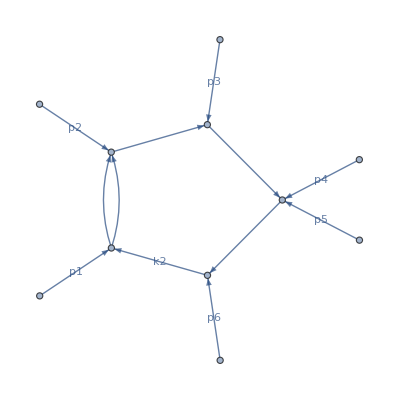

```mathematica
PureIntegralsOld[[142]]
PureIntegralsOld[[154]]
plotDiagram[PureIntegralsOld[[142]]]
```

```mathematica
q[1]=p[1]+p[2]/.p4cons;
q[2]=p[6]/.p4cons;
q[3]=p[4]+p[5]/.p4cons;
q[4]=-q[1]-q[2]-q[3];
intMasses={msq[1]->0,msq[2]->0,msq[3]->mt2,msq[4]->0};
modcayleyMat=Table[CayleyEntry[i,j],{i,1,4},{j,1,4}];
modcayleyMat//MatrixForm
kP=3+1;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]/.root[x_]:>root[Factor[x]]/.root[x_^2 y_^2]:>x y
BasisChange[7]=ep^3/LS (1-2ep)

q[1]=p[1]/.p4cons;
q[2]=p[6]/.p4cons;
q[3]=p[4]+p[5];
q[4]=p[3]/.p4cons;
q[5]=-q[1]-q[2]-q[3]-q[4];
intMasses={msq[1]->0,msq[2]->0,msq[3]->mt2,msq[4]->0,msq[5]->0};
modcayleyMat=Table[CayleyEntry[i,j],{i,0,5},{j,0,5}];
modcayleyMat//MatrixForm
kP=4;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]/.root[x_]:>root[-x]

vectors={q[1],q[2],q[3],q[4]};
Gram1=Det[Expand[Table[vectors[[i]]vectors[[j]],{i,1,4},{j,1,4}]]/.kinematics/.mandelstamScalarProducts];
vectors2={q[1],q[2],q[3],q[4],k[2]};
Baikov=Factor[Expand[Det[Expand[Table[vectors2[[i]]vectors2[[j]],{i,1,5},{j,1,5}]]/.loopMomentumScalarProducts/.kinematics/.mandelstamScalarProducts]]];

BasisChange[8]=ep^4/LS 1/PR[2]*(2*Baikov)/(Gram1*(d-4));
```

(0 | -s12 | mt2-s345 | 0
-s12 | 0 | 0 | -s123
mt2-s345 | 0 | 2 mt2 | mt2-s45
0 | -s123 | mt2-s45 | 0)

1/(2 root[(mt2 s12-mt2 s123+s123 s345-s12 s45)^2])

2 (1-2 ep) ep^3 root[(mt2 s12-mt2 s123+s123 s345-s12 s45)^2]

(0 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | mt2-s16 | -s23 | 0
1 | 0 | 0 | 0 | -s123 | -s12
1 | mt2-s16 | 0 | 2 mt2 | mt2-s45 | mt2-s345
1 | -s23 | -s123 | mt2-s45 | 0 | 0
1 | 0 | -s12 | mt2-s345 | 0 | 0)

1/(2 root[s12^2 s16^2-2 s12 s123 s16^2+s123^2 s16^2+2 mt2 s12 s16 s23-2 s12^2 s16 s23-2 mt2 s123 s16 s23+2 s12 s123 s16 s23+mt2^2 s23^2-2 mt2 s12 s23^2+s12^2 s23^2+2 s12 s123 s16 s345-2 s123^2 s16 s345-4 mt2 s12 s23 s345+2 mt2 s123 s23 s345+2 s12 s123 s23 s345+2 s12 s16 s23 s345+2 s123 s16 s23 s345-2 mt2 s23^2 s345-2 s12 s23^2 s345+s123^2 s345^2-2 s123 s23 s345^2+s23^2 s345^2-2 s12^2 s16 s45+2 s12 s123 s16 s45+2 mt2 s12 s23 s45-2 s12^2 s23 s45-4 s12 s16 s23 s45-2 s12 s123 s345 s45+2 s12 s23 s345 s45+s12^2 s45^2])

# Diagram 143/155 (Basis1 - 138)

hxb[-1,1,0,1,1,1,1,1,0,0,0,0,0]

hxb[0,1,0,1,1,1,1,1,0,0,0,0,0]

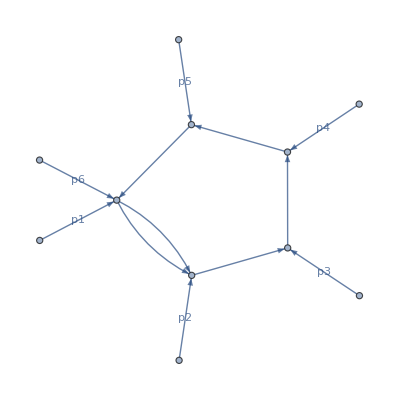

```mathematica
PureIntegralsOld[[143]]
PureIntegralsOld[[155]]
plotDiagram[PureIntegralsOld[[143]]]
```

```mathematica
q[1]=p[1]+p[2]+p[6]/.p4cons;
q[2]=p[3]/.p4cons;
q[3]=p[4]/.p4cons;
q[4]=-q[1]-q[2]-q[3];
intMasses={msq[1]->mt2,msq[2]->0,msq[3]->0,msq[4]->0};
modcayleyMat=Table[CayleyEntry[i,j],{i,1,4},{j,1,4}];
modcayleyMat//MatrixForm
kP=3+1;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]/.root[x_]:>root[Factor[x]]/.root[x_^2 y_^2]:>x y
BasisChange[9]=ep^3/LS (1-2ep)

q[1]=p[1]+p[6]/.p4cons;
q[2]=p[2]/.p4cons;
q[3]=p[3];
q[4]=p[4]/.p4cons;
q[5]=-q[1]-q[2]-q[3]-q[4];
intMasses={msq[1]->mt2,msq[2]->0,msq[3]->0,msq[4]->0,msq[5]->0};
modcayleyMat=Table[CayleyEntry[i,j],{i,0,5},{j,0,5}];
modcayleyMat//MatrixForm
kP=4;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]/.root[x_]:>root[-x]

vectors={q[1],q[2],q[3],q[4]};
Gram1=Det[Expand[Table[vectors[[i]]vectors[[j]],{i,1,4},{j,1,4}]]/.kinematics/.mandelstamScalarProducts];
vectors2={q[1],q[2],q[3],q[4],k[2]};
Baikov=Factor[Expand[Det[Expand[Table[vectors2[[i]]vectors2[[j]],{i,1,5},{j,1,5}]]/.loopMomentumScalarProducts/.kinematics/.mandelstamScalarProducts]]];

BasisChange[10]=ep^4/LS 1/PR[2]*(2*Baikov)/(Gram1*(d-4));
```

(2 mt2 | mt2-s345 | mt2-s45 | 0
mt2-s345 | 0 | 0 | -s34
mt2-s45 | 0 | 0 | 0
0 | -s34 | 0 | 0)

1/(2 s34 (mt2-s45))

2 (1-2 ep) ep^3 s34 (mt2-s45)

(0 | 1 | 1 | 1 | 1 | 1
1 | 2 mt2 | mt2-s16 | mt2-s345 | mt2-s45 | 0
1 | mt2-s16 | 0 | 0 | -s23 | -s234
1 | mt2-s345 | 0 | 0 | 0 | -s34
1 | mt2-s45 | -s23 | 0 | 0 | 0
1 | 0 | -s234 | -s34 | 0 | 0)

1/(2 root[mt2^2 s23^2+2 mt2 s16 s23 s34-2 mt2 s23^2 s34+s16^2 s34^2-2 s16 s23 s34^2+s23^2 s34^2-2 mt2 s23^2 s345+2 mt2 s23 s234 s345-4 mt2 s23 s34 s345+2 s16 s23 s34 s345-2 s23^2 s34 s345-2 s16 s234 s34 s345+2 s23 s234 s34 s345+s23^2 s345^2-2 s23 s234 s345^2+s234^2 s345^2-2 mt2 s23 s234 s45+2 mt2 s23 s34 s45-4 s16 s23 s34 s45+2 s16 s234 s34 s45+2 s23 s234 s34 s45-2 s16 s34^2 s45-2 s23 s34^2 s45+2 s23 s234 s345 s45-2 s234^2 s345 s45+2 s23 s34 s345 s45+2 s234 s34 s345 s45+s234^2 s45^2-2 s234 s34 s45^2+s34^2 s45^2])

# Diagram 164/165 (Basis1 - 138)

hxb[1,0,0,1,1,1,1,1,-1,0,0,0,0]

hxb[1,0,0,1,1,1,1,1,0,0,0,0,0]

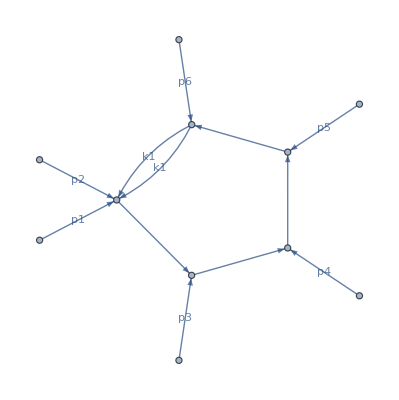

```mathematica
PureIntegralsOld[[164]]
PureIntegralsOld[[165]]
plotDiagram[PureIntegralsOld[[164]]]
```

```mathematica
q[1]=p[1]+p[2]+p[6]/.p4cons;
q[2]=p[3]/.p4cons;
q[3]=p[4]/.p4cons;
q[4]=-q[1]-q[2]-q[3];
intMasses={msq[1]->mt2,msq[2]->0,msq[3]->0,msq[4]->0};
modcayleyMat=Table[CayleyEntry[i,j],{i,1,4},{j,1,4}];
modcayleyMat//MatrixForm
kP=3+1;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]/.root[x_]:>root[Factor[x]]/.root[x_^2 y_^2]:>x y
BasisChange[11]=ep^3/LS (1-2ep)

q[1]=p[1]+p[2]/.p4cons;
q[2]=p[3]/.p4cons;
q[3]=p[4];
q[4]=p[5]/.p4cons;
q[5]=-q[1]-q[2]-q[3]-q[4];
intMasses={msq[1]->0,msq[2]->0,msq[3]->0,msq[4]->0,msq[5]->mt2};
modcayleyMat=Table[CayleyEntry[i,j],{i,0,5},{j,0,5}];
modcayleyMat//MatrixForm
kP=4;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]/.root[x_]:>root[-x]

vectors={q[1],q[2],q[3],q[4]};
Gram1=Det[Expand[Table[vectors[[i]]vectors[[j]],{i,1,4},{j,1,4}]]/.kinematics/.mandelstamScalarProducts];
vectors2={q[1],q[2],q[3],q[4],k[2]};
Baikov=Factor[Expand[Det[Expand[Table[vectors2[[i]]vectors2[[j]],{i,1,5},{j,1,5}]]/.loopMomentumScalarProducts/.kinematics/.mandelstamScalarProducts]]];

BasisChange[12]=ep^4/LS 1/PR[1]*(2*Baikov)/(Gram1*(d-4));
```

(2 mt2 | mt2-s345 | mt2-s45 | 0
mt2-s345 | 0 | 0 | -s34
mt2-s45 | 0 | 0 | 0
0 | -s34 | 0 | 0)

1/(2 s34 (mt2-s45))

2 (1-2 ep) ep^3 s34 (mt2-s45)

(0 | 1 | 1 | 1 | 1 | 1
1 | 0 | -s12 | -s123 | -s56 | 0
1 | -s12 | 0 | 0 | -s34 | mt2-s345
1 | -s123 | 0 | 0 | 0 | mt2-s45
1 | -s56 | -s34 | 0 | 0 | 0
1 | 0 | mt2-s345 | mt2-s45 | 0 | 2 mt2)

1/(2 root[mt2^2 s12^2-2 mt2^2 s12 s123+mt2^2 s123^2-2 mt2^2 s12 s34+2 mt2^2 s123 s34+2 mt2 s12 s123 s34-2 mt2 s123^2 s34+mt2^2 s34^2-2 mt2 s123 s34^2+s123^2 s34^2+2 mt2 s12 s123 s345-2 mt2 s123^2 s345-2 mt2 s123 s34 s345-2 s123^2 s34 s345+s123^2 s345^2-2 mt2 s12^2 s45+2 mt2 s12 s123 s45+4 mt2 s12 s34 s45-2 mt2 s123 s34 s45+2 s12 s123 s34 s45-2 mt2 s34^2 s45-2 s123 s34^2 s45-2 s12 s123 s345 s45+2 s123 s34 s345 s45+s12^2 s45^2-2 s12 s34 s45^2+s34^2 s45^2-2 mt2 s12 s345 s56+2 mt2 s123 s345 s56-2 mt2 s34 s345 s56+2 s123 s34 s345 s56-2 s123 s345^2 s56+2 mt2 s12 s45 s56-2 mt2 s123 s45 s56+2 mt2 s34 s45 s56-4 s12 s34 s45 s56+2 s123 s34 s45 s56+2 s12 s345 s45 s56+2 s123 s345 s45 s56+2 s34 s345 s45 s56-2 s12 s45^2 s56-2 s34 s45^2 s56+s345^2 s56^2-2 s345 s45 s56^2+s45^2 s56^2])

# Diagram 144 (Basis1 - 138)

hxb[-1,1,0,1,1,1,1,1,1,0,0,0,0]

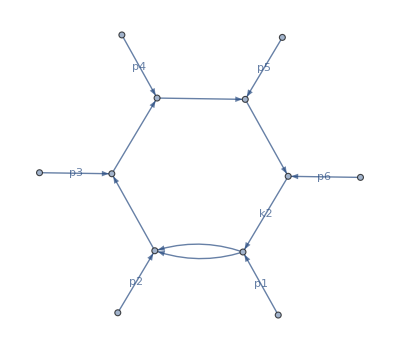

```mathematica
PureIntegralsOld[[144]]
plotDiagram[PureIntegralsOld[[144]]]
```

```mathematica
q[1]=p[1]+p[2]/.p4cons;
q[2]=p[3]/.p4cons;
q[3]=p[4];
q[4]=p[5]/.p4cons;
q[5]=-q[1]-q[2]-q[3]-q[4];
intMasses={msq[1]->0,msq[2]->0,msq[3]->0,msq[4]->0,msq[5]->mt2};
modcayleyMat=Table[CayleyEntry[i,j],{i,0,5},{j,0,5}];
modcayleyMat//MatrixForm
kP=4;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]/.root[x_]:>root[-x]

vectors={q[1],q[2],q[3],q[4]};
Gram1=Det[Expand[Table[vectors[[i]]vectors[[j]],{i,1,4},{j,1,4}]]/.kinematics/.mandelstamScalarProducts];
vectors2={q[1],q[2],q[3],q[4],k[2]};
Baikov=Factor[Expand[Det[Expand[Table[vectors2[[i]]vectors2[[j]],{i,1,5},{j,1,5}]]/.loopMomentumScalarProducts/.kinematics/.mandelstamScalarProducts]]];

BasisChange[13]=ep^4/LS *1/PR[1](1-2ep)*(2*Baikov)/(Gram1*(d-4));
```

(0 | 1 | 1 | 1 | 1 | 1
1 | 0 | -s12 | -s123 | -s56 | 0
1 | -s12 | 0 | 0 | -s34 | mt2-s345
1 | -s123 | 0 | 0 | 0 | mt2-s45
1 | -s56 | -s34 | 0 | 0 | 0
1 | 0 | mt2-s345 | mt2-s45 | 0 | 2 mt2)

1/(2 root[mt2^2 s12^2-2 mt2^2 s12 s123+mt2^2 s123^2-2 mt2^2 s12 s34+2 mt2^2 s123 s34+2 mt2 s12 s123 s34-2 mt2 s123^2 s34+mt2^2 s34^2-2 mt2 s123 s34^2+s123^2 s34^2+2 mt2 s12 s123 s345-2 mt2 s123^2 s345-2 mt2 s123 s34 s345-2 s123^2 s34 s345+s123^2 s345^2-2 mt2 s12^2 s45+2 mt2 s12 s123 s45+4 mt2 s12 s34 s45-2 mt2 s123 s34 s45+2 s12 s123 s34 s45-2 mt2 s34^2 s45-2 s123 s34^2 s45-2 s12 s123 s345 s45+2 s123 s34 s345 s45+s12^2 s45^2-2 s12 s34 s45^2+s34^2 s45^2-2 mt2 s12 s345 s56+2 mt2 s123 s345 s56-2 mt2 s34 s345 s56+2 s123 s34 s345 s56-2 s123 s345^2 s56+2 mt2 s12 s45 s56-2 mt2 s123 s45 s56+2 mt2 s34 s45 s56-4 s12 s34 s45 s56+2 s123 s34 s45 s56+2 s12 s345 s45 s56+2 s123 s345 s45 s56+2 s34 s345 s45 s56-2 s12 s45^2 s56-2 s34 s45^2 s56+s345^2 s56^2-2 s345 s45 s56^2+s45^2 s56^2])

# Gram Change

```mathematica
CanonicalGramVec={p[1],p[2],p[3],p[4]};
Ganonical5ptGram=16Det[Expand[Table[CanonicalGramVec[[i]]CanonicalGramVec[[j]],{i,1,4},{j,1,4}]]/.kinematics/.mandelstamScalarProducts]//Factor
vectors={p[3],p[4],p[5],p[6]};
Gram1=16Det[Expand[Table[vectors[[i]]vectors[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;
GramChange1=16Det[Expand[Table[vectors[[i]]CanonicalGramVec[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;

vectors={p[4],p[5],p[6],p[1]};
Gram2=16Det[Expand[Table[vectors[[i]]vectors[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;
GramChange2=16Det[Expand[Table[vectors[[i]]CanonicalGramVec[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;

vectors={p[5],p[6],p[1],p[2]};
Gram3=16Det[Expand[Table[vectors[[i]]vectors[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;
GramChange3=16Det[Expand[Table[vectors[[i]]CanonicalGramVec[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;

vectors={p[3],p[2],p[1],p[6]};
Gram4=16Det[Expand[Table[vectors[[i]]vectors[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;
GramChange4=16Det[Expand[Table[vectors[[i]]CanonicalGramVec[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;

vectors={p[2],p[3],p[4],p[5]};
Gram5=16Det[Expand[Table[vectors[[i]]vectors[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;
GramChange5=16Det[Expand[Table[vectors[[i]]CanonicalGramVec[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;

vectors={p[3],p[4],p[5],p[6]};
Gram6=16Det[Expand[Table[vectors[[i]]vectors[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;
GramChange6=16Det[Expand[Table[vectors[[i]]CanonicalGramVec[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;


Gram5Repl={root[Gram1]->GramChange1/root[Ganonical5ptGram],root[Gram2]->GramChange2/root[Ganonical5ptGram],root[Gram3]->GramChange3/root[Ganonical5ptGram],root[Gram4]->GramChange4/root[Ganonical5ptGram],root[Gram5]->GramChange5/root[Ganonical5ptGram],root[Gram6]->GramChange6/root[Ganonical5ptGram]};
```

s12^2 s23^2-2 s12^2 s23 s234+2 s12 s123 s23 s234+s12^2 s234^2-2 s12 s123 s234^2+s123^2 s234^2+2 s12 s123 s23 s34-2 s12 s23^2 s34+2 s12 s123 s234 s34-2 s123^2 s234 s34+2 s12 s23 s234 s34+2 s123 s23 s234 s34+s123^2 s34^2-2 s123 s23 s34^2+s23^2 s34^2-2 s12 s23^2 s56+2 s12 s23 s234 s56-2 s123 s23 s234 s56-4 s12 s23 s34 s56+2 s123 s23 s34 s56-2 s23^2 s34 s56+s23^2 s56^2

# Assemble basis

```mathematica
SelectInts={7,8,9,10,11,12,13,14,15,16,17,20,21,23,24,25,26,27,29,30,31,33,59,60,75,76,77,78,79,81,82,83,84,89,90,112,113,114,115,116,117,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,151,140,152,141,153,142,154,143,155,164,165,144};
SelectIntsNotPure=Pick[SelectInts,Thread[SelectInts>138]]
SelectIntsPure=Pick[SelectInts,Thread[SelectInts<=138]]

PureIntegralsNew[[139]]=Collect[PureIntegralsOld[[151]]*BasisChange[1]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[151]]=Collect[PureIntegralsOld[[151]]*BasisChange[2]//Expand,{_hxb,root[___]},Together];

PureIntegralsNew[[140]]=Collect[PureIntegralsOld[[152]]*BasisChange[3]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[152]]=Collect[PureIntegralsOld[[152]]*BasisChange[4]//Expand,{_hxb,root[___]},Together];

PureIntegralsNew[[141]]=Collect[PureIntegralsOld[[153]]*BasisChange[5]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[153]]=Collect[PureIntegralsOld[[153]]*BasisChange[6]//Expand,{_hxb,root[___]},Together];

PureIntegralsNew[[142]]=Collect[PureIntegralsOld[[154]]*BasisChange[7]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[154]]=Collect[PureIntegralsOld[[154]]*BasisChange[8]//Expand,{_hxb,root[___]},Together];

PureIntegralsNew[[142]]=Collect[PureIntegralsOld[[154]]*BasisChange[7]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[154]]=Collect[PureIntegralsOld[[154]]*BasisChange[8]//Expand,{_hxb,root[___]},Together];

PureIntegralsNew[[143]]=Collect[PureIntegralsOld[[155]]*BasisChange[9]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[155]]=Collect[PureIntegralsOld[[155]]*BasisChange[10]//Expand,{_hxb,root[___]},Together];

PureIntegralsNew[[164]]=Collect[PureIntegralsOld[[165]]*BasisChange[11]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[165]]=Collect[PureIntegralsOld[[165]]*BasisChange[12]//Expand,{_hxb,root[___]},Together];

PureIntegralsNew[[144]]=Collect[PureIntegralsOld[[144]]*BasisChange[13]//Expand,{_hxb,root[___]},Together];

(*PureIntegralsNew[[162]]=Collect[PureIntegralsOld[[162]]*BasisChange[17]//Expand,{_hxb,root[___]},Together];*)
SubPureInts=PureIntegralsNew[[SelectInts]]/.Gram5Repl;
Newsqrts=(Cases[SubPureInts,root[___],Infinity]//DeleteDuplicates)/.root[x_]:>x
Oldsqrts=(Cases[PureIntegralsOld/.Gram5Repl,root[___],Infinity]//DeleteDuplicates)/.root[x_]:>x
sqrtSetNew=Join[Oldsqrts,Newsqrts]//DeleteDuplicates;
Export[FileNameJoin[{Directory[],"files/Roots.txt"}],sqrtSetNew];
Export[FileNameJoin[{NotebookDirectory[],"BubblePureInts.txt"}],SubPureInts];
```

{139,151,140,152,141,153,142,154,143,155,164,165,144}

{7,8,9,10,11,12,13,14,15,16,17,20,21,23,24,25,26,27,29,30,31,33,59,60,75,76,77,78,79,81,82,83,84,89,90,112,113,114,115,116,117,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138}

{(-s12+s34)^2-2 (s12+s34) s56+s56^2,-4 s12 s23 s34 (-s123+s23-s234+s56)+(-s12 s23+s12 s234-s123 s234+s123 s34-s23 s34+s23 s56)^2,-4 mt2 s12+(-mt2-s12+s345)^2,mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2,s345^2-2 s345 s45+s45^2,mt2^2-2 mt2 s16+s16^2-2 mt2 s234-2 s16 s234+s234^2,-4 mt2 s56+s56^2,mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2,s16^2-2 s16 s23+s23^2-2 s16 s45-2 s23 s45+s45^2,s56 (-4 mt2 s12 s34+(mt2-s345)^2 s56),s56 (-4 mt2 s12 s34+mt2^2 s56-2 mt2 s345 s56+s345^2 s56),s12^2 s23^2-2 s12^2 s23 s234+2 s12 s123 s23 s234+s12^2 s234^2-2 s12 s123 s234^2+s123^2 s234^2+2 s12 s123 s23 s34-2 s12 s23^2 s34+2 s12 s123 s234 s34-2 s123^2 s234 s34+2 s12 s23 s234 s34+2 s123 s23 s234 s34+s123^2 s34^2-2 s123 s23 s34^2+s23^2 s34^2-2 s12 s23^2 s56+2 s12 s23 s234 s56-2 s123 s23 s234 s56-4 s12 s23 s34 s56+2 s123 s23 s34 s56-2 s23^2 s34 s56+s23^2 s56^2,(mt2 s12-mt2 s123+s123 s345-s12 s45)^2}

{(-s12+s34)^2-2 (s12+s34) s56+s56^2,-4 s12 s23 s34 (-s123+s23-s234+s56)+(-s12 s23+s12 s234-s123 s234+s123 s34-s23 s34+s23 s56)^2,-4 mt2 s12+(-mt2-s12+s345)^2,-4 mt2 s56+s56^2,mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2,mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2,-4 mt2 s12 s34 s56+mt2^2 s56^2-2 mt2 s345 s56^2+s345^2 s56^2,s12^2 s23^2-2 s12^2 s23 s234+2 s12 s123 s23 s234+s12^2 s234^2-2 s12 s123 s234^2+s123^2 s234^2+2 s12 s123 s23 s34-2 s12 s23^2 s34+2 s12 s123 s234 s34-2 s123^2 s234 s34+2 s12 s23 s234 s34+2 s123 s23 s234 s34+s123^2 s34^2-2 s123 s23 s34^2+s23^2 s34^2-2 s12 s23^2 s56+2 s12 s23 s234 s56-2 s123 s23 s234 s56-4 s12 s23 s34 s56+2 s123 s23 s34 s56-2 s23^2 s34 s56+s23^2 s56^2,s345^2-2 s345 s45+s45^2,mt2^2-2 mt2 s16+s16^2-2 mt2 s234-2 s16 s234+s234^2,s16^2-2 s16 s23+s23^2-2 s16 s45-2 s23 s45+s45^2,s56 (-4 mt2 s12 s34+(mt2-s345)^2 s56),s56 (-4 mt2 s12 s34+mt2^2 s56-2 mt2 s345 s56+s345^2 s56)}

# Export New Basis

```mathematica
StillNonPureInts=DeleteElements[PureIntegralsOld[[139;;]],PureIntegralsOld[[SelectIntsNotPure]]];
NewPureInts=PureIntegralsNew[[SelectIntsNotPure]];
NewBasis=Join[PureIntegralsNew[[;;138]],NewPureInts,StillNonPureInts]//EchoFunction[Length];
NewBasis=NewBasis/.Gram5Repl;
Newsqrts=(Cases[NewBasis,root[___],Infinity]//DeleteDuplicates)/.root[x_]:>x
Export[FileNameJoin[{Directory[],"files/Roots.txt"}],Newsqrts];

Export[FileNameJoin[{Directory[],"files/PureIntegralBasis1-151.txt"}],NewBasis];
```

241

{(-s12+s34)^2-2 (s12+s34) s56+s56^2,-4 s12 s23 s34 (-s123+s23-s234+s56)+(-s12 s23+s12 s234-s123 s234+s123 s34-s23 s34+s23 s56)^2,-4 mt2 s12+(-mt2-s12+s345)^2,-4 mt2 s56+s56^2,mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2,mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2,-4 mt2 s12 s34 s56+mt2^2 s56^2-2 mt2 s345 s56^2+s345^2 s56^2,s12^2 s23^2-2 s12^2 s23 s234+2 s12 s123 s23 s234+s12^2 s234^2-2 s12 s123 s234^2+s123^2 s234^2+2 s12 s123 s23 s34-2 s12 s23^2 s34+2 s12 s123 s234 s34-2 s123^2 s234 s34+2 s12 s23 s234 s34+2 s123 s23 s234 s34+s123^2 s34^2-2 s123 s23 s34^2+s23^2 s34^2-2 s12 s23^2 s56+2 s12 s23 s234 s56-2 s123 s23 s234 s56-4 s12 s23 s34 s56+2 s123 s23 s34 s56-2 s23^2 s34 s56+s23^2 s56^2,s345^2-2 s345 s45+s45^2,mt2^2-2 mt2 s16+s16^2-2 mt2 s234-2 s16 s234+s234^2,s16^2-2 s16 s23+s23^2-2 s16 s45-2 s23 s45+s45^2,s56 (-4 mt2 s12 s34+(mt2-s345)^2 s56),s56 (-4 mt2 s12 s34+mt2^2 s56-2 mt2 s345 s56+s345^2 s56),(mt2 s12-mt2 s123+s123 s345-s12 s45)^2}

```mathematica
NewBasis[[151]]
```